```mathematica
(* Project Euler Problem 171 *)
```

```mathematica
mxnum =10^6;
sqrlim=9^2Log10[mxnum];
sqrs=Table[i^2,{i,1,Ceiling[Sqrt[sqrlim]]}];
sumsqrs=Table[Total[IntegerDigits[n]^2],{n,1,mxnum}];
tal=Tally[sumsqrs];
snms=Intersection[sqrs,Transpose[tal][[1]]];

(* Start fixing here *)
pos=Position[Transpose[tal][[1]],snms];
dvls=Transpose[tal][[2]][[Flatten[pos]]]
Total[dvls]
```

{}

0

```mathematica
snms
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,441}

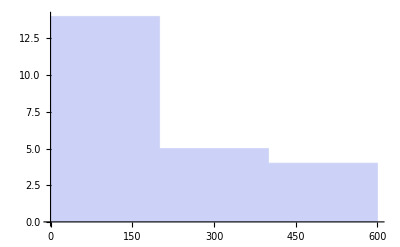

```mathematica
Histogram[sqrs]
```

```mathematica
(* Think of this problem as finding all possibe partitions of the squares less than sqrlim in terms of sums of squares*)
```

```mathematica
(* Try PowersRepresentations too *)
```